```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
CCFws[d_,decorframe_]:=
Module[
{dir =d,
ndc=decorframe},
(*{np, dt,rt}=ParticleTimeSeries[d,"rods"];*)
{np,dt,rt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,rt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
distsT=Table[Norm[{rt[[t,i,3]],rt[[t,i,4]]}],{t,Length[rt]},{i,Length[rt[[t]]]}];
firstRod=Ceiling[Length[rt[[1]]]/4];
lastRod=Floor[Length[rt[[1]]]*3/4];
corrs=Table[{SetPrecision[Total[distsT[[t,i;;j]]],1],
Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Ceiling[Length[rt]/2],Length[rt],ndc},
{i,firstRod,lastRod},
{j,i,lastRod}];
gatheredCoors = Gather[Flatten[corrs,2],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
errs=Table[StandardDeviation[gatheredCoors[[i,All,2]]]/Sqrt[Length[gatheredCoors[[i]]]],{i,Length[gatheredCoors]}];
Clear[rt,anglesT,corrs,gatheredCoors];
{ccf,errs}
];
CCF[d_,decorframe_,firstframe_:1,lastframe_:-1]:=
Module[
{dir =d,
ndc=decorframe,
ff=firstframe,
lf=lastframe},
(*{np, dt,rt}=ParticleTimeSeries[d,"rods"];*)
{np,dt,rt}=ParticleTimeSeries[d,"links"];
nlinksT=Table[Length[l],{l,rt}];
fracture=Position[nlinksT,Except[Head[nlinksT]|nlinksT[[1]]],1,1];
fractureT=If[Length[fracture]>0, fracture[[1,1]],Length[rt]];
rt=rt[[1;;fractureT]];
If[lf>Length[rt] ||ff<1||lf<ff && lf>0,Print["Inappropriate Frame bounds; Using whole series"],rt=rt[[ff;;lf]]];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
ld=Sqrt[rt[[1,1,3]]^2+rt[[1,1,4]]^2];
firstRod=Ceiling[Length[rt[[1]]]/4];
lastRod=Floor[Length[rt[[1]]]*3/4];
corrs=Table[{(j-i)*ld,
Cos[anglesT[[t,j]]-anglesT[[t,i]]]},{t,Ceiling[Length[rt]/2],Length[rt],ndc},
{i,firstRod,lastRod},
{j,i,lastRod}];
gatheredCoors = Gather[Flatten[corrs,2],First[#1]==First[#2]&];
ccf=Table[Mean[gc],{gc,gatheredCoors}];
errs=Table[StandardDeviation[gatheredCoors[[i,All,2]]]/Sqrt[Length[gatheredCoors[[i]]]],{i,Length[gatheredCoors]}];
Clear[rt,anglesT,corrs,gatheredCoors];
{ccf,errs}
];
plFits[ccfTab_,LpPredTab_,finaldp_:-1]:=
Table[
NonlinearModelFit[
ccfTab[[i,1,2;;finaldp]],
Exp[-x/(2*Lp)],
{{Lp,LpPredTab[[i]]}},
x,
Weights->1/ccfTab[[i,2,2;;finaldp]]^2
],
{i,1,Length[ccfTab]}
];
plLinFits[ccfTab_]:=
Table[
LinearModelFit[
MapAt[
Function[x,Log[x]],
Pick[ccfTab[[j,1]],Positive[ccfTab[[j,1,All,2]]]],Table[{i,2},{i,Length[Pick[ccfTab[[j,1]],Positive[ccfTab[[j,1,All,2]]]]]}]
],
x,
x
],
{j,1,Length[ccfTab]}
];
allplots[ccftab_,nmfittab_,lmfittab_,plotrange_,titles_]:=Table[
Show[
LogPlot[
Normal[nmfittab[[i]]]/.x->l,{l,0.001,100},
PlotStyle->{Black},PlotRange->plotrange
],
LogPlot[
Exp[Normal[lmfittab[[i]]]]/.x->l,{l,0.001,100},
PlotStyle->{Red},PlotRange->plotrange
],
ListLogPlot[ccftab[[i,1]],PlotRange->plotrange],Frame->True,FrameLabel->{"r(μm)","<Cos(θ(x+r)-θ(x))>",titles[[i]]},BaseStyle->{FontSize->14}
]
,{i,Min[Length[titles],Length[nmfittab],Length[lmfittab],Length[ccftab]]}];
```

## Backward Bending + BAOAB

```mathematica
seeds=Table[ToString[i],{i,4421,4440}];
basedir="nm200_bwd_bend_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfs=ParallelTable[CCF[dr,100],{dr,dirs[[2;;]]}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_bwd_bend_seed4421/txt_stack/links.txt

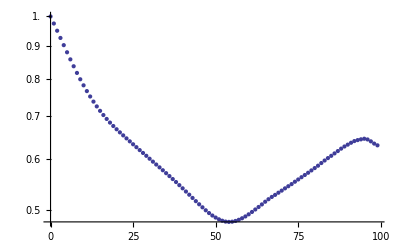

```mathematica
ListLogPlot[ccf[[1,1]]]
```

```mathematica
tNMfits=plFits[ccf,Table[10,{Length[ccf]}],30];
tLinFits=plLinFits[ccf];
tPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,tNMfits}];
```

```mathematica
tPls
```

{22.9182}

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
ts=Map[Function[x,"Seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds[[1;;1]],tPls}]];
```

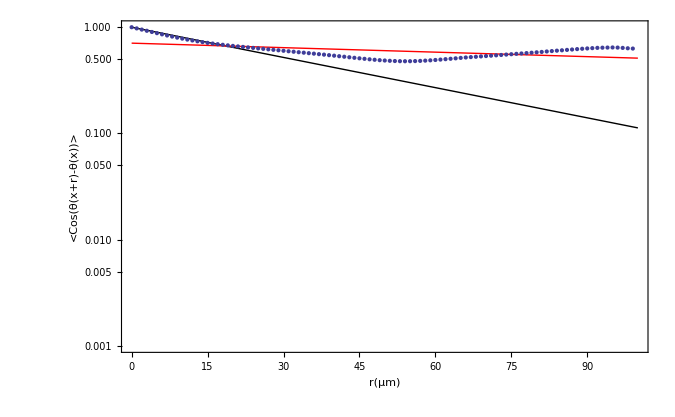

```mathematica
allplots[ccf,tNMfits,tLinFits,pr,ts]
```

## Longer Simulation

```mathematica
seeds=Table[ToString[i],{i,4401,4424}];
basedir="nm200_BDlong_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfs=ParallelTable[CCF[dr,100],{dr,dirs}];
```

```mathematica
tNMfits=plFits[ccfs,Table[10,{Length[ccfs]}],11];
tLinFits=plLinFits[ccfs];
tPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,tNMfits}];
```

```mathematica
tPls
```

{11.3627,11.4193,10.9876,10.9393,10.3573,10.9218,12.7725,11.2189,11.9416,11.8402,13.5515,12.513,10.6688,11.1962,12.3315,12.1317,11.874,11.3465,12.7869,11.5227,12.5584,11.1254,11.6675,11.8583}

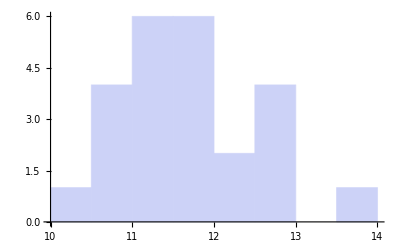

```mathematica
Histogram[tPls,7]
```

```mathematica
Mean[tPls]
```

11.7039

```mathematica
StandardDeviation[tPls]
```

0.768934

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
ts=Map[Function[x,"Seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds,tPls}]];
```

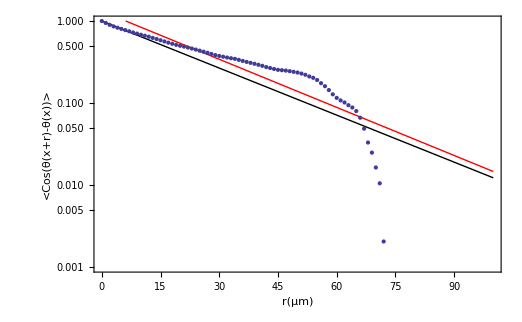
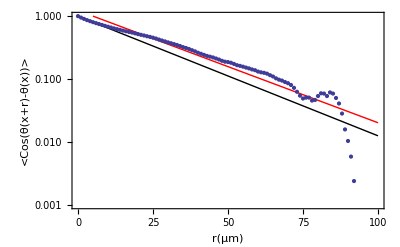
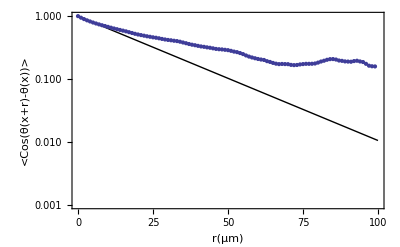
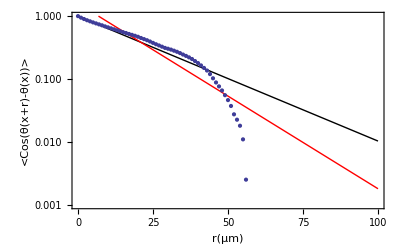
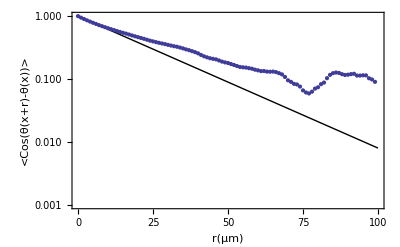
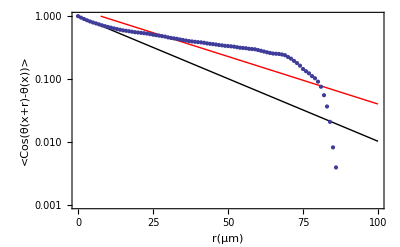
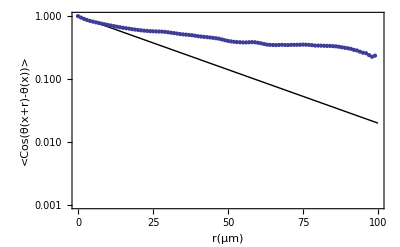
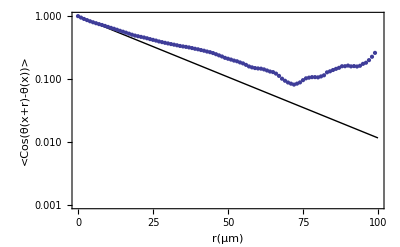

```mathematica
allplots[ccfs,tNMfits,tLinFits,pr,ts]
```

## Low Friction Ensemble, Higher Stiffness

```mathematica
seeds=Table[ToString[i],{i,4401,4450}];
basedir="nm200_BD_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfBDs1=ParallelTable[CCF[dr,100],{dr,dirs}];
```

```mathematica
seeds=Table[ToString[i],{i,4451,4496}];
basedir="nm200_BD_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfBDs2=ParallelTable[CCF[dr,100],{dr,dirs}];
```

```mathematica
seeds=Table[ToString[i],{i,4401,4500}];
ccfBDs=Join[ccfBDs1,ccfBDs2];
```

```mathematica
bdNMfits=plFits[ccfBDs,Table[10,{2*Length[seeds]}],10];
```

```mathematica
bdLinFits=plLinFits[ccfBDs];
```

```mathematica
bdPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,bdNMfits}];
```

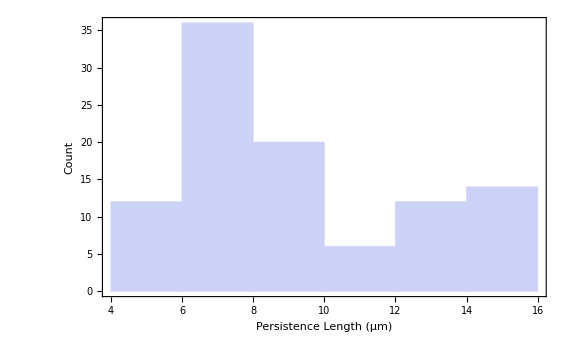

```mathematica
Histogram[bdPls,Frame->True,FrameLabel->{"Persistence Length (μm)","Count","Ensemble of Low Friction Persistence Length Simulation \n(1 Simulation per dp)"},BaseStyle->{FontSize->16}]
```

```mathematica
Mean[bdPls]
```

9.2198

```mathematica
15.74902700483186
```

```mathematica
StandardDeviation[bdPls]
```

3.02731

```mathematica
3.709513728194964
```

```mathematica
Median[bdPls]
```

8.27575

```mathematica
tot=Total[ccfBDs];
```

Total::tllen: Lists of unequal length in {« 1 »} cannot be added.

```mathematica
ts=Map[Function[x,"Seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds,bdPls}]];
```

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
allplots[ccfBDs,bdNMfits,bdLinFits,pr,ts]
```

## Time Equilibration of Persistence Length Measurement

```mathematica
seeds=Table[ToString[i],{i,4301,4400}];
basedir="nm200_BD_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
dirs[[24]]
```

/home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_BD_seed4324

```mathematica
timeframes=Join[Table[{i,i+9},{i,1,91,10}],Table[{i,i+99},{i,101,901,100}],Table[{i,i+999},{i,1001,9001,1000}]];
ccfTimes=ParallelTable[CCF[dirs[[-1]],1,t[[1]],t[[2]]],{t,timeframes}];
```

```mathematica
tNMfits=plFits[ccfTimes,Table[10,{Length[timeframes]}],11];
tLinFits=plLinFits[ccfTimes];
tPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,tNMfits}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
timeframes2=Join[Table[{i,i+9},{i,5001,5091,10}],Table[{i,i+99},{i,5101,5901,100}],Table[{i,i+999},{i,5001,9001,1000}]];
```

```mathematica
ccfTimes2=ParallelTable[CCF[dirs[[24]],1,t[[1]],t[[2]]],{t,timeframes2}];
tNMfits2=plFits[ccfTimes2,Table[10,{Length[timeframes2]}],11];
tLinFits2=plLinFits[ccfTimes2];
tPls2=Table[nm["ParameterTableEntries"][[1,1]],{nm,tNMfits2}];
```

```mathematica
dirs[[-1]]
```

/home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_BD_seed4400

```mathematica
ccfTimes3=ParallelTable[CCF[dirs[[-1]],1,t[[1]],t[[2]]],{t,timeframes2}];
tNMfits3=plFits[ccfTimes3,Table[10,{Length[timeframes2]}],11];
tLinFits3=plLinFits[ccfTimes3];
tPls3=Table[nm["ParameterTableEntries"][[1,1]],{nm,tNMfits3}];
```

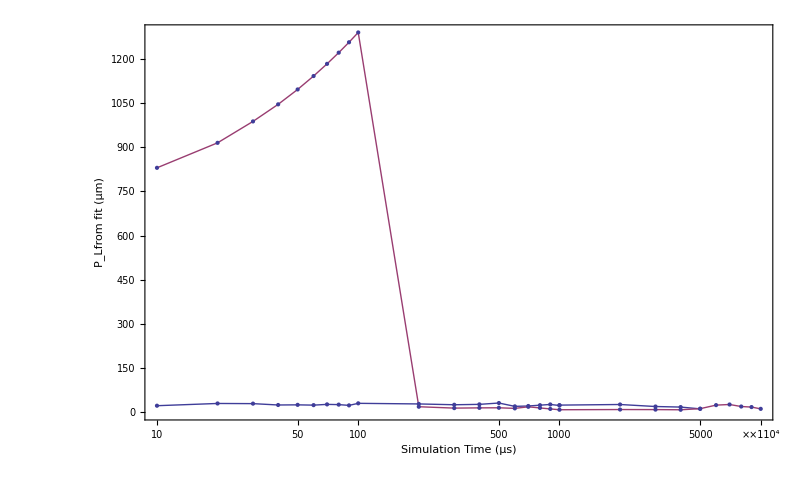

```mathematica
ListLogLinearPlot[{Transpose[{Max/@timeframes2-5000,tPls3}],Transpose[{Max/@timeframes,tPls}]},Frame->True,FrameLabel->{"Simulation Time (μs)","P_Lfrom fit (μm)","Equilibration of Persistence Length Measurement"},BaseStyle->{FontSize->16},Joined->True,Mesh->All,PlotRange->Full]
```

## Low Friction Ensemble, Langevin LeapFrog

```mathematica
seeds=Table[ToString[i],{i,4301,4350}];
basedir="nm200_LLF_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfLLFs=ParallelTable[CCF[dr,100],{dr,dirs}];
```

```mathematica
llfNMfits=plFits[ccfLLFs,Table[10,{Length[seeds]}],10];
```

```mathematica
llfLinFits=plLinFits[ccfLLFs];
```

```mathematica
llfPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,llfNMfits}];
```

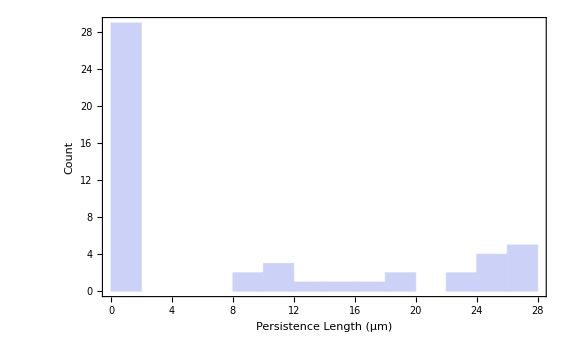

```mathematica
Histogram[llfPls,10,Frame->True,FrameLabel->{"Persistence Length (μm)","Count","Ensemble of Low Friction Persistence Length Simulation \n(1 Simulation per dp)"},BaseStyle->{FontSize->16}]
```

```mathematica
llfPls
```

{10.914,24.765,14.9177,9.9311,25.5446,25.9834,27.1942,18.7823,27.1074,26.7813,26.6644,25.2666,11.0975,18.7586,23.0717,26.4342,23.5602,17.1698,12.1707,0.00453736,0.00667082,0.0119389,0.0125944,0.0126139,0.0119725,0.0124829,0.0128364,0.0125029,0.0125509,0.0114012,0.012278,0.000398881,0.0128182,0.0128285,0.00507655,0.0120142,0.0126909,0.0116445,0.0102491,0.0115783,0.0113537,0.00447953,0.0118092,0.0116962,0.0127746,0.00296685,0.0114427,0.00727675,11.5788,9.33873}

```mathematica
tot=Total[ccfLLFs];
```

Total::tllen: Lists of unequal length in {« 1 »} cannot be added.

```mathematica
ts=Map[Function[x,"Seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds,llfPls}]];
```

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
allplots[ccfLLFs,llfNMfits,llfLinFits,pr,ts]
```

## Low Friction Ensemble, Bending Modulus fixed

```mathematica
seeds=Table[ToString[i],{i,4351,4366}];
basedir="nm200_BD_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfwsBDs=ParallelTable[CCFws[dr,100],{dr,dirs}];
```

StandardDeviation::shlen: The argument {1.} should have at least two elements.

StandardDeviation::shlen: The argument {0.999744} should have at least two elements.

StandardDeviation::shlen: The argument {1.} should have at least two elements.

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_BD_seed4352/txt_stack/links.txt

StandardDeviation::shlen: The argument {1.} should have at least two elements.

StandardDeviation::shlen: The argument {0.999744} should have at least two elements.

General::stop: Further output of StandardDeviation :: shlen will be suppressed during this calculation.

```mathematica
bdNMfitsws=plFits[ccfwsBDs,Table[10,{Length[seeds]}],10];
```

```mathematica
bdLinFitsws=plLinFits[ccfwsBDs];
```

```mathematica
bdPlsws=Table[nm["ParameterTableEntries"][[1,1]],{nm,bdNMfitsws}];
```

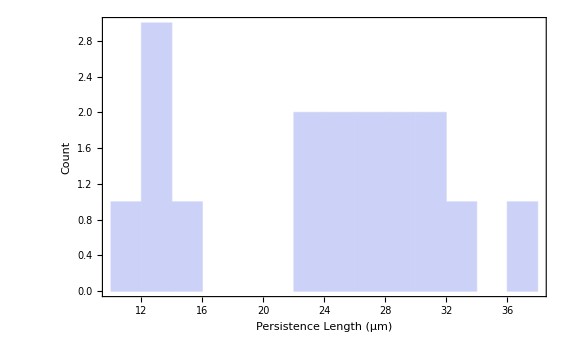

```mathematica
Histogram[bdPlsws,10,Frame->True,FrameLabel->{"Persistence Length (μm)","Count","Ensemble of Low Friction Persistence Length Simulation \n(1 Simulation per dp)"},BaseStyle->{FontSize->16}]
```

```mathematica
tot=Total[ccfBDs];
```

Total::tllen: Lists of unequal length in {« 1 »} cannot be added.

```mathematica
ts=Map[Function[x,"Seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds,bdPls}]];
```

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
allplots[ccfBDs,bdNMfits,bdLinFits,pr,ts]
```

## Low Friction Ensemble, Bending Modulus fixed

```mathematica
seeds=Table[ToString[i],{i,4301,4350}];
basedir="nm200_BD_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfBDs2=ParallelTable[CCF[dr,100],{dr,dirs}];
```

```mathematica
seeds=Table[ToString[i],{i,4351,4400}];
basedir="nm200_BD_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
ccfBDs=ParallelTable[CCF[dr,100],{dr,dirs}];
```

```mathematica
ccfBDs1=ccfBDs;
```

```mathematica
seeds=Table[ToString[i],{i,4301,4400}];
```

```mathematica
ccfBDs=Join[ccfBDs1,ccfBDs2];
```

```mathematica
bdNMfits=plFits[ccfBDs,Table[10,{2*Length[seeds]}],10];
```

```mathematica
bdLinFits=plLinFits[ccfBDs];
```

```mathematica
bdPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,bdNMfits}];
```

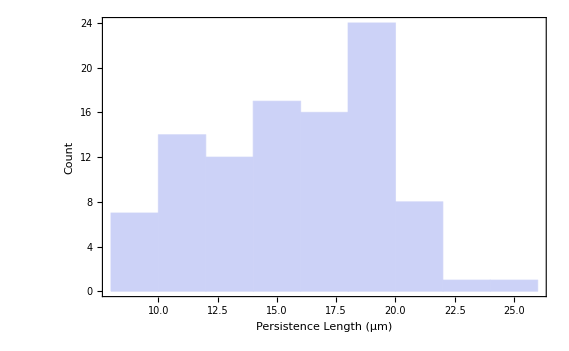

```mathematica
Histogram[bdPls,Frame->True,FrameLabel->{"Persistence Length (μm)","Count","Ensemble of Low Friction Persistence Length Simulation \n(1 Simulation per dp)"},BaseStyle->{FontSize->16}]
```

```mathematica
Mean[bdPls]
```

```mathematica
15.74902700483186
```

```mathematica
StandardDeviation[bdPls]
```

```mathematica
3.709513728194964
```

```mathematica
Median[bdPls]
```

16.3362

```mathematica
tot=Total[ccfBDs];
```

Total::tllen: Lists of unequal length in {« 1 »} cannot be added.

```mathematica
ts=Map[Function[x,"Seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds,bdPls}]];
```

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
allplots[ccfBDs,bdNMfits,bdLinFits,pr,ts]
```

## Varying Stretching Stiffness

```mathematica
kt=.004; (*pN-um*)
```

```mathematica
SetAccuracy[90,3]
```

90.

```mathematica
kls=Join[Range[.01,.10,.01],Range[.20,1.00,.1],Range[2,10,1],Range[20,100,10]];
```

```mathematica
klsts={".01",".02",".03",".04",".05",".06",".07",".08",".09",".10",".20",".30",".40",".50",".60",".70",".80",".90","1.00","2.00","3.00","4.00","5.00","6.00","7.00","8.00","9.00","10.00","20.00","30.00","40.00","50.00","60.00","70.00","80.00","90.00","100.00"};
basedir="nm200_kl";
dirs=Table[mdwlcl<>basedir<>k,{k,klsts}];
```

```mathematica
ccfKls=ParallelTable[CCF[dr,1000],{dr,dirs}];
```

```mathematica
Table[Length[ccfKls[[i,2]]],{i,Length[klsts]}]
```

{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
klNMfits=plFits[ccfKls,Table[10,{Length[klsts]}],20];
```

```mathematica
klLinFits=plLinFits[ccfKls];
```

```mathematica
klPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,klNMfits}];
```

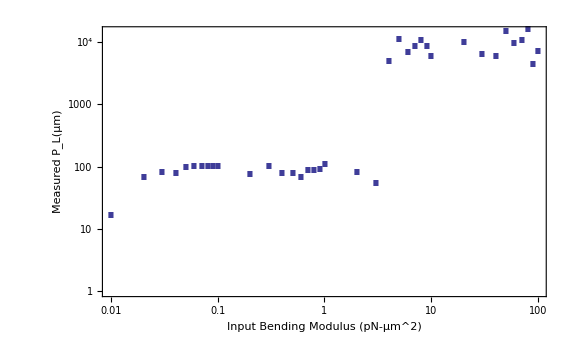

```mathematica
ListLogLogPlot[Transpose[{ToExpression@klsts,klPls}],PlotRange->{{0,1},{0,500}},Frame->True,FrameLabel->{"Input Bending Modulus (pN-μm^2)","Measured P_L(μm)"},BaseStyle->{FontSize->16},PlotMarkers->{"·",50}]
```

```mathematica
ccfSpringy=CCFws[dirs[[1]],1000];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_kl.01/txt_stack/links.txt

StandardDeviation::shlen: The argument {1.} should have at least two elements.

```mathematica
nmfitspringy=plFits[{ccfSpringy},Table[10,{1}],20];
springylinfit=plLinFits[{ccfSpringy}];
```

```mathematica
nmfitspringy[[1]]["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 23.3988 | 1.80666 | 12.9514 | 1.46359×10^-10

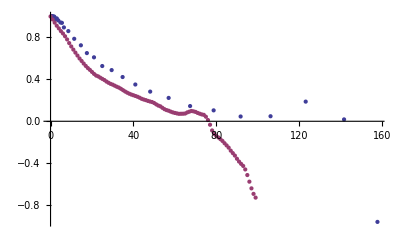

```mathematica
ListPlot[{ccfSpringy[[1]],ccfKls[[1,1]]}]
```

```mathematica
ts=Map[Function[x,"k_L = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{klsts,klPls}]];
```

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
allplots[ccfKls,klNMfits,klLinFits,pr,ts]
```

## Varying Bending Modulus

```mathematica
kt=.004; (*pN-um*)
```

```mathematica
kapbs={".0001",".0002",".0003",".0004",".0005",".0006",".0007",".0008",".0009",".0010",".0020",".0030",".0040",".0050",".0060",".0070",".0080",".0090",
".0100",".0200",".0300",".0400",".0500",".0600",".0700",".0800",".0900",
".1000",".2000",".3000",".4000",".5000",".6000",".7000",".8000",".9000",
"1.0000"};
basedir="nm200_kapb";
dirs=Table[mdwlcl<>basedir<>k,{k,kapbs}];
```

```mathematica
ccfKaps=ParallelTable[CCF[dr,1000],{dr,dirs}];
```

```mathematica
Table[Length[ccfKaps[[i,2]]],{i,Length[kapbs]}]
```

{100,100,100,100,100,100,100,100,91,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
kbNMfits=plFits[ccfKaps,Table[ToExpression[kb]/kt,{kb,kapbs}],50];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
kbLinFits=plLinFits[ccfKaps];
```

```mathematica
kbPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,kbNMfits}];
```

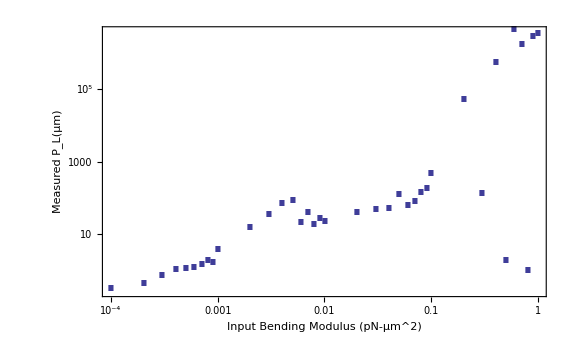

```mathematica
ListLogLogPlot[Transpose[{ToExpression@kapbs,kbPls}],PlotRange->{{0,1},{0,500}},Frame->True,FrameLabel->{"Input Bending Modulus (pN-μm^2)","Measured P_L(μm)"},BaseStyle->{FontSize->16},PlotMarkers->{"·",50}]
```

```mathematica
ts=Map[Function[x,"κ_B = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{kapbs,kbPls}]];
```

```mathematica
pr={{0,100},{0.001,1}};
```

```mathematica
allplots[ccfKaps,kbNMfits,kbLinFits,pr,ts]
```

## Low Friction Ensemble

```mathematica
seeds=Table[ToString[i],{i,4001,4016}];
basedir="nm200_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
Length[ccfSeeds]
```

16

```mathematica
lfNMfits=plFits[ccfSeeds,Table[10,{Length[seeds]}],50];
```

```mathematica
lfLinFits=plLinFits[ccfSeeds];
```

```mathematica
fricPls=Table[nm["ParameterTableEntries"][[1,1]],{nm,lfNMfits}];
```

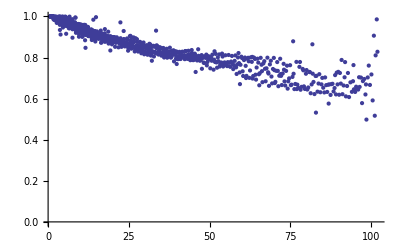

```mathematica
ListPlot[ccfSeeds[[2,1]],PlotRange->Full]
```

```mathematica
ts=Map[Function[x,"seed = "<>Part[x,1]<>"; L_p = "<>ToString[Part[x,2]]<>" μm"],Transpose[{seeds,fricPls}]];
```

```mathematica
Length[ts]
```

100

```mathematica
pr={{0,100},{10^-3,1}};
```

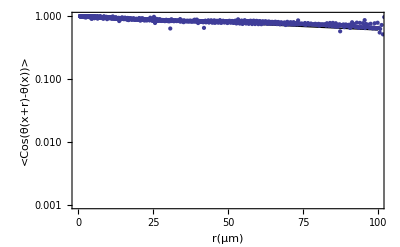
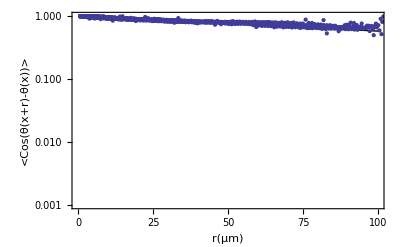
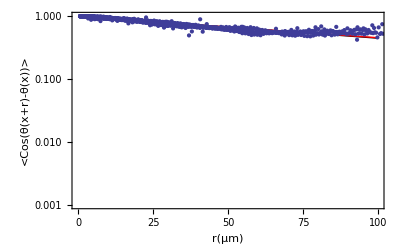
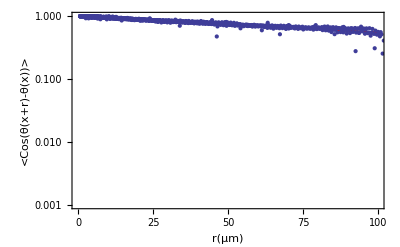
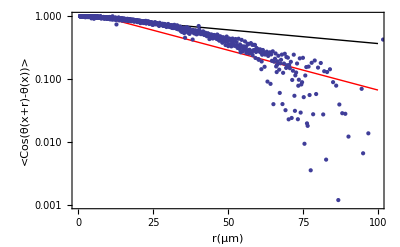
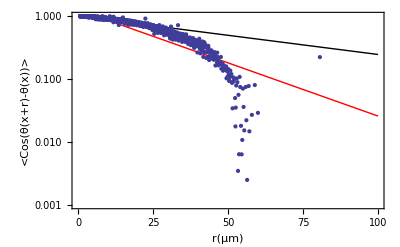
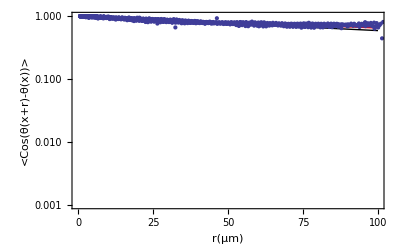
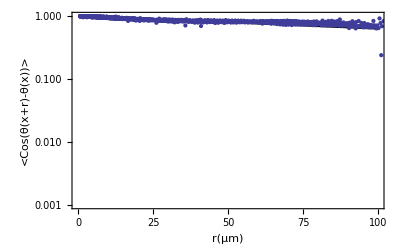

```mathematica
allplots[ccfSeeds,lfNMfits,lfLinFits,pr,ts]
```

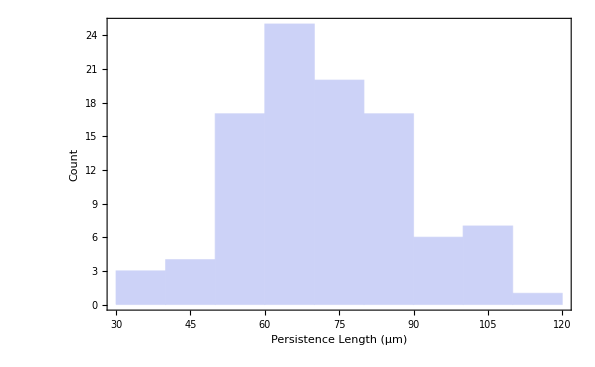

```mathematica
Histogram[fricPls,10,Frame->True,FrameLabel->{"Persistence Length (μm)","Count","Ensemble of Low Friction Persistence Length Simulation \n(1 Simulation per dp)"},BaseStyle->{FontSize->16}]
```

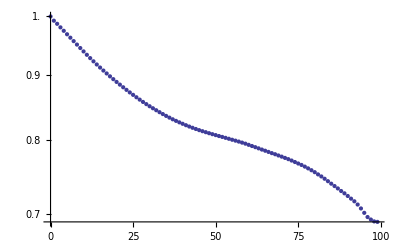

```mathematica
ListLogPlot[ccs[[1]]]
```

## Ensemble of Motor Spring Stiffness

```mathematica
lowKaps={".04",".08",".12",".16",".20",".24",".28",".32",".36",".40",".44",".48",".52",".56",".60",".64",".68",".72",".76",".80",".84",".88",".92",".96","1.00","1.04","1.08","1.12","1.16","1.20","1.24","1.28","1.32","1.36","1.40","1.44","1.48","1.52","1.56","1.60","1.64","1.68","1.72","1.76","1.80","1.84","1.88","1.92"};
higherKaps={".5","1.0","1.5","2.0","2.5","3.0","3.5","4.0","4.5","5.0","5.5","6.0","6.5","7.0","7.5","8.0","8.5","9.0","9.5","10.0","10.5","11.0","11.5","12.0","12.5","13.0","13.5","14.0","14.5","15.0","15.5","16.0","16.5","17.0","17.5","18.0","18.5","19.0","19.5","20.0","20.5","21.0","21.5","22.0","22.5","23.0","23.5","24.0"};
kaps={"30","50","70","90","110","130","150","170","190"};
basedir="nm50_linear_bend_kapb";
dirs=Table[mdwlcl<>basedir<>s,{s,kaps}];
```

```mathematica
kaps={".001",".002",".003",".004",".005",".006",".007",".008",".009",
".010",".020",".030",".040",".050",".060",".070",".080",".090",
".100",".200",".300",".400",".500",".600",".700",".800",".900",
"1.000","2.000","3.000","4.000","5.000","6.000","7.000","8.000","9.000","10.000"};
basedir="nm200_kapb";
dirs=Table[mdwlcl<>basedir<>s,{s,kaps}];
```

```mathematica
kT=.004;
```

```mathematica
ccfs=Table[CCF[dr,10],{dr,dirs[[1;;10]]}];
```

```mathematica
ccfsBar=ccfs;
```

```mathematica
ccfsBar=Table[{MovingAverage[ccfs[[i,1]],10],MovingAverage[ccfs[[i,2]],2]},{i,Length[ccfs]}];
```

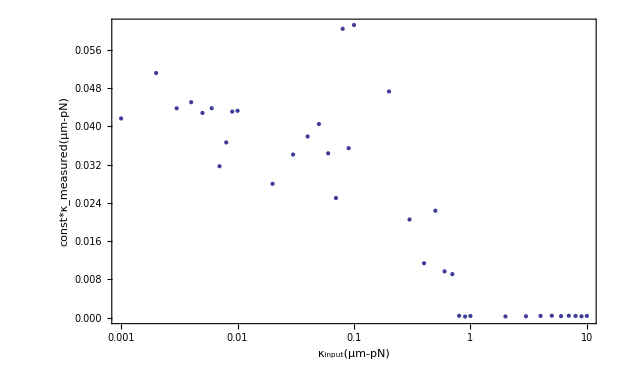

```mathematica
kappakappa=Table[{ToExpression[kaps[[i]]],nlms[[i]]["ParameterTableEntries"][[1,1]]*.004},{i,Length[kaps]}];
ListLogLinearPlot[kappakappa,Frame->True,FrameLabel->{"κ_input(μm-pN)","const*κ_measured(μm-pN)","Linear forcing springs"},PlotRange->Full,BaseStyle->{FontSize->16}]
```

```mathematica
LinearModelFit[kappakappa,x,x]
```

FittedModel[0.0057112+0.000476014 x]

```mathematica
1/.000476
```

2100.84

```mathematica
2100*.04
```

84.

```mathematica
0.4/0.011
```

36.3636

```mathematica
20*0.04
```

0.8

```mathematica
scale
```

416.

```mathematica
Table[{nlms[[i]]["ParameterTable"],seeds[[i]]},{i,Length[nlms]}]//TableForm
```

```mathematica
Histogram[Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}],100,Frame->True, FrameLabel->{"Lp(um)","counts","Distribution of persistence lengths as measured by CCF"},BaseStyle->{FontSize->16}]
```

```mathematica
pls=Table[nlms[[i]]["ParameterTableEntries"][[1,1]],{i,Length[nlms]}];
```

```mathematica
Mean[pls]
```

64.7173

```mathematica
Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]
```

40

```mathematica
meanccfs=Total[ccfs[[All,1,1;;Min[Table[Length[ccfs[[i,1]]],{i,Length[ccfs]}]]]]]/Length[ccfs];
```

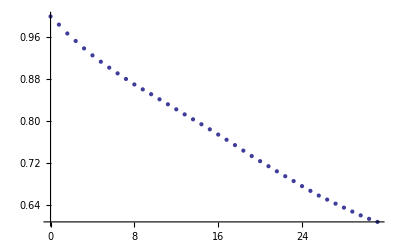

```mathematica
ListPlot[meanccfs]
```

```mathematica
nlm=NonlinearModelFit[
meanccfs,
Exp[-x/(2Lp)],
{Lp},
x];
```

```mathematica
nlm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
Lp | 30.7481 | 0.123067 | 249.849 | 4.11909×10^-64

```mathematica
Series[Cos[x],{x,0,4}]
```

1-x^2/2+x^4/24+O[x]^5

```mathematica
Series[Sqrt[1-x],{x,0,4}]
```

1-x/2-x^2/8-x^3/16-(5 x^4)/128+O[x]^5

```mathematica
FullSimplify[(1-Cos[θ/2])]
```

2 Sin[θ/4]^2

```mathematica
Series[1-2Cos[x/2]+Cos[x/2]^2,{x,0,6}]
```

x^4/64-x^6/1536+O[x]^7

```mathematica
Cos[π-x]
```

-Cos[x]

```mathematica
FullSimplify[1/2(1+Cos[θ])]
```

Cos[θ/2]^2

LinkObject::linkd: Unable to communicate with closed link LinkObject["/software/mathematica-9.0-x86_64/Executables/math -subkernel -noinit -mathlink", 1645, 18].

KernelObject::rdead: Subkernel connected through KernelObject[15, "local"] appears dead.

LaunchKernels::clone: Kernel KernelObject[15, "local", "<defunct>"] resurrected as KernelObject[15, "local"].

$Aborted